#### Notebook Description

This notebook is for brain storming.

#### Project Goals

Construct a symbolic representation of a chessboard state (ChessState) and chess moves (ChessMove) in the Wolfram Language.
Develop a function which takes a ChessState and a ChessPlay and returns the new ChessState.
Build a ConvertChessNotation function for converting between the Wolfram and the algebraic chess notation.
Curate a Chess Dataset of famous chess games in the history for the data repository.
Create a ChessStatePlot function which plots a given ChessState on a chessboard. 
Create a ChessMovePlot function that plots the transition from the inputted ChessState to the next state specified by a ChessMove, alongside with a ChessAnimate function that animates a chess game (a dataset or a list of ChessMove’s).
Depending on the amount of remaining time, write a ListGameMove function that receives a ChessState (and ChessRules) and outputs all the possible ChessMove’s. 
Potentially, provide Evaluate → True/”Best” option for ListChessMove which returns sorted and associate predicted winning probabilities/scores for white using an external game engine.
Note: This project will be done keeping in mind that eventually the word Chess in the above functions would be replaced by the word Game, generalizing to as many board and card games possible.

### Chess Pieces

#### Chess Piece Names

```mathematica
If[
	NotebookDirectory[] ≠ ""
	, 
	packageDir = NotebookDirectory[];
	,
	packageDir = $InputFileName;
]
packageDir
```

/home/miladiouss/MiladBox/Mathematica/WSS18/Summer2018Starter/ChessPackage/

```mathematica
pieceNamesShort = {"King", "Queen", "Rook", "Bishop", "Knight", "Pawn"};
wpn = Table["White" <> pieceName, {pieceName, pieceNamesShort}];
bpn = Table["Black" <> pieceName, {pieceName, pieceNamesShort}];
pieceNames = wpn ~Join~ bpn;
AppendTo[pieceNames, "EmptySquare"];
```

```mathematica
whitePieces = {"♔", "♕", "♖", "♗", "♘", "♙"};
blackPieces = {"♚", "♛", "♜", "♝", "♞", "♟"} ;
pieceSymbols = whitePieces ~Join~ blackPieces ~Join~ {"□"};
{♔, ♕, ♖, ♗, ♘, ♙, ♚, ♛, ♜, ♝, ♞, ♟, □} = pieceSymbols;
(*{♔, ♕, ♖, ♗, ♘, ♙, ♚, ♛, ♜, ♝, ♞, ♟, □} = pieceNames;*)
```

#### Download/Load Chess Piece Images

```mathematica
If[
	FileExistsQ[packageDir <> "pieceImages.mx"]
	,
	pieceImages = Import[NotebookDirectory[] <> "pieceImages.mx"];
	Print["Chess piece images were loaded."];
	,
	piecePicLinksWiki =
		{
		"https://upload.wikimedia.org/wikipedia/commons/thumb/4/42/Chess_klt45.svg/75px-Chess_klt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/1/15/Chess_qlt45.svg/75px-Chess_qlt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/7/72/Chess_rlt45.svg/75px-Chess_rlt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/b/b1/Chess_blt45.svg/75px-Chess_blt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/7/70/Chess_nlt45.svg/75px-Chess_nlt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/4/45/Chess_plt45.svg/75px-Chess_plt45.svg.png"
		} ~Join~
		{
		"https://upload.wikimedia.org/wikipedia/commons/thumb/f/f0/Chess_kdt45.svg/75px-Chess_kdt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/4/47/Chess_qdt45.svg/75px-Chess_qdt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/f/ff/Chess_rdt45.svg/75px-Chess_rdt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/9/98/Chess_bdt45.svg/75px-Chess_bdt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/e/ef/Chess_ndt45.svg/75px-Chess_ndt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/c/c7/Chess_pdt45.svg/75px-Chess_pdt45.svg.png"
		};

	imagePicMotherLink = "https://marcelk.net/chess/pieces/merida/320/";
	piecePicLinks = Table["https://marcelk.net/chess/pieces/merida/320/" <> pieceName <> ".png", {pieceName, Most @ pieceNames}];

	pieceImages = 
		Import /@ piecePicLinks;
	AppendTo[pieceImages, Graphics[{Hue[0, 0, 1, 0], Rectangle[]}, ImageSize -> ImageDimensions @ First @ pieceImages]];
	Export[NotebookDirectory[]<>"pieceImages.mx",pieceImages];
	Print["Chess piece images were downloaded."];
]
```

Chess piece images were loaded.

#### Chess Piece Object

```mathematica
pieceObj = 
	MapThread[
		#1 -> <|"Name" -> #2, "Symbol" -> #3, "Image" -> #4|>&,
		{pieceSymbols, pieceNames, pieceSymbols, pieceImages}
	];
	
pieceObj = Association @ pieceObj;
```

Example of using pieceObj:

```mathematica
ImageResize[pieceObj[♔]["Image"],50]
pieceObj[♔]["Symbol"]
```

-Graphics-

♔

### Setups

#### Setup Initial Chess State

```mathematica
files = {"a", "b", "c", "d", "e", "f", "g", "h"};
fileSize = Length @ files;
ranks = {"1", "2", "3", "4", "5", "6", "7", "8"};
rankSize = Length @ ranks;

emptyBoard = Table[Mod[i + j, 2], {i, 8}, {j, 8}];
bottomLeftBlackBoard = Table[Mod[i + j    , 2], {i, 8}, {j, 8}];
bottomLeftWhiteBoard = Table[Mod[i + j + 1, 2], {i, 8}, {j, 8}];

(* Black Coordinate Matrix *)
bcm = ({{"a8", "b8", "c8", "d8", "e8", "f8", "g8", "h8"}, {"a7", "b7", "c7", "d7", "e7", "f7", "g7", "h7"}, {"a6", "b6", "c6", "d6", "e6", "f6", "g6", "h6"}, {"a5", "b5", "c5", "d5", "e5", "f5", "g5", "h5"}, {"a4", "b4", "c4", "d4", "e4", "f4", "g4", "h4"}, {"a3", "b3", "c3", "d3", "e3", "f3", "g3", "h3"}, {"a2", "b2", "c2", "d2", "e2", "f2", "g2", "h2"}, {"a1", "b1", "c1", "d1", "e1", "f1", "g1", "h1"}});
(* White Coordinate Matrix *)
wcm = Reverse[bcm];
(* Usage: Position[wcm, "e1"]//First; *)

stateMatrix0 = ({{♜, ♞, ♝, ♛, ♚, ♝, ♞, ♜}, {♟, ♟, ♟, ♟, ♟, ♟, ♟, ♟}, {□, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □}, {♙, ♙, ♙, ♙, ♙, ♙, ♙, ♙}, {♖, ♘, ♗, ♕, ♔, ♗, ♘, ♖}});


initialChessStateList = Thread[Flatten[bcm] -> Flatten[stateMatrix0]];
initialChessStateList = initialChessStateList ~Join~ {"♖♔" -> True, "♔♖" -> True, "♜♚" -> True, "♚♜" -> True, "EnPassant" -> None};
AppendTo[initialChessStateList, "WhiteCemetery" -> {}];
AppendTo[initialChessStateList, "BlackCemetery" -> {}];
AppendTo[initialChessStateList, "Turn" -> "White"];
AppendTo[initialChessStateList, "Result" -> {}];
initialChessStateList
```

{a8→♜,b8→♞,c8→♝,d8→♛,e8→♚,f8→♝,g8→♞,h8→♜,a7→♟,b7→♟,c7→♟,d7→♟,e7→♟,f7→♟,g7→♟,h7→♟,a6→□,b6→□,c6→□,d6→□,e6→□,f6→□,g6→□,h6→□,a5→□,b5→□,c5→□,d5→□,e5→□,f5→□,g5→□,h5→□,a4→□,b4→□,c4→□,d4→□,e4→□,f4→□,g4→□,h4→□,a3→□,b3→□,c3→□,d3→□,e3→□,f3→□,g3→□,h3→□,a2→♙,b2→♙,c2→♙,d2→♙,e2→♙,f2→♙,g2→♙,h2→♙,a1→♖,b1→♘,c1→♗,d1→♕,e1→♔,f1→♗,g1→♘,h1→♖,♖♔→True,♔♖→True,♜♚→True,♚♜→True,EnPassant→None,WhiteCemetery→{},BlackCemetery→{},Turn→White,Result→{}}

<| a8 -> ♜, b8 -> ♞, ..., a6 -> □, ..., h1 -> ♖,
♖♔ -> True, ♔♖ -> True, ♜♚ -> True, ♚♜ -> True, EnPassant -> None, 
WhiteCemetery -> { }, BlackCemetery -> { }, Turn -> White, Result -> { } |>

```mathematica
ChessState[a_?AssociationQ][pos_?StringQ] /; StringMatchQ[pos, files ~~ ranks] := Lookup[a, pos, □]
ChessState[a_?AssociationQ][i_Integer, j_Integer] := ChessState[a][files⟦i⟧ <> ranks⟦j⟧]
ChessState[a_?AssociationQ][{i_Integer, j_Integer}] := ChessState[a][i, j]
(*ChessState /: ChessState[a_?AssociationQ][pos_?StringQ] /; StringMatchQ[pos, files ~~ ranks] = v_ := ChessState*)
ChessState /: MakeBoxes[cs_ChessState, StandardForm] := 
	Module[{icon},
		icon = 
			ToBoxes[
				ImageResize[
					(*pieceObj[♞]["Image"]*)
					Rasterize[ChessPlot[cs, "MatrixForm"-> True]]
					, 
					300
				]
		];
			
		InterpretationBox @@ 
			{
				RowBox[{"ChessState", "[", icon, "]"}],
			cs
			}
	]
```

```mathematica
cs0 = ChessState[Association@initialChessStateList];
```

Example of using ChessState:

```mathematica
Quit
```

```mathematica
cs0
cs0["g1"]
cs0[5, 8]
cs0[{5, 8}]
ChessPlot[cs0, "MatrixForm" -> True]
First[cs0]
```

ChessState[-Graphics-]

♘

♚

♚

(♜ | ♞ | ♝ | ♛ | ♚ | ♝ | ♞ | ♜
♟ | ♟ | ♟ | ♟ | ♟ | ♟ | ♟ | ♟
□ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □
♙ | ♙ | ♙ | ♙ | ♙ | ♙ | ♙ | ♙
♖ | ♘ | ♗ | ♕ | ♔ | ♗ | ♘ | ♖)

<|a8→♜,b8→♞,c8→♝,d8→♛,e8→♚,f8→♝,g8→♞,h8→♜,a7→♟,b7→♟,c7→♟,d7→♟,e7→♟,f7→♟,g7→♟,h7→♟,a6→□,b6→□,c6→□,d6→□,e6→□,f6→□,g6→□,h6→□,a5→□,b5→□,c5→□,d5→□,e5→□,f5→□,g5→□,h5→□,a4→□,b4→□,c4→□,d4→□,e4→□,f4→□,g4→□,h4→□,a3→□,b3→□,c3→□,d3→□,e3→□,f3→□,g3→□,h3→□,a2→♙,b2→♙,c2→♙,d2→♙,e2→♙,f2→♙,g2→♙,h2→♙,a1→♖,b1→♘,c1→♗,d1→♕,e1→♔,f1→♗,g1→♘,h1→♖,WhiteCemetery→{},BlackCemetery→{},♖♔→True,♔♖→True,♜♚→True,♚♜→True|>

### ChessPlot

```mathematica
tabulatePieceInset[insetToAlgFunc_, chessState_] :=
	Table[
		Inset[
			pieceObj[chessState[insetToAlgFunc[i, j]]]["Image"], 
			{i, j} - {1, 1}, 
			{i, j} - {1, 1}, 
			1
		]
		,
		{i, 8}
		, 
		{j, 8}
	];
			
tabulateCoordInset[insetToAlgFunc_] := 
	Table[
		Inset[
			Text[Style[insetToAlgFunc[i, j], 7]], 
			{i, j} + {-0.12, -0.09},
			Automatic,
			1
		]
		,
		{i, 8}
		,
		{j, 8}
	];
		

(* White -> Down, Origin is a1 *)
whiteDownCoordTable = 
	tabulateCoordInset[{i, j} ↦ files⟦i⟧ <> ranks⟦j⟧];
(* White -> Up, Origin is h8 *)
whiteUpCoordTable = 
	tabulateCoordInset[{i, j} ↦ files⟦9 - i⟧ <> ranks⟦9 - j⟧];
(* White -> Left, Origin is h1 *)
whiteLeftCoordTable = 
	tabulateCoordInset[{i, j} ↦ files⟦9 - j⟧ <> ranks⟦i⟧];
(* White -> right, Origin is a8 *)
whiteRightCoordTable =
	tabulateCoordInset[{i, j} ↦ files⟦j⟧ <> ranks⟦9 - i⟧];
		
Options[ChessPlot] = Join[
	{"WhiteOrientation" -> Automatic, "BoardColorSet" -> Automatic, "ShowCoordinates" -> True, "MatrixForm" -> False},
	Options[ArrayPlot]
];

ChessPlot[chessState_, opts: OptionsPattern[]] :=
	
	Module[{cs = First[chessState], pieceInset, coordInset, insetList, emptyBoard, plot, LightSquareColor, DarkSquareColor},
		(* Matrix Form *)
		If[OptionValue["MatrixForm"], 
			Return[
				MatrixForm[Partition[Values[cs⟦ ;; rankSize fileSize⟧], Length[files]]]
			]
		];
		
		(* Board Orientation *)
		Switch[
			OptionValue["WhiteOrientation"],
			Automatic | "Down",
				pieceInset = tabulatePieceInset[{i, j} ↦ files⟦i⟧ <> ranks⟦j⟧, cs];
				coordInset = whiteDownCoordTable;
				emptyBoard = bottomLeftBlackBoard;
			,
			"Up",
				pieceInset = tabulatePieceInset[{i, j} ↦ files⟦9 - i⟧ <> ranks⟦9 - j⟧, cs];
				coordInset = whiteUpCoordTable;
				emptyBoard = bottomLeftBlackBoard;
			,
			"Left",
				pieceInset = tabulatePieceInset[{i, j} ↦ files⟦9 - j⟧ <> ranks⟦i⟧, cs];
				coordInset = whiteLeftCoordTable;
				emptyBoard = bottomLeftWhiteBoard;
			,
			"Right",
				pieceInset = tabulatePieceInset[{i, j} ↦ files⟦j⟧ <> ranks⟦9 - i⟧, cs];
				coordInset = whiteRightCoordTable;
				emptyBoard = bottomLeftWhiteBoard;
			,
			_,
				Print["Wrong \"WhiteOrientation\" option was provided. Try \"Up\" for instance."]; Return[$Failed];
		];
		
		(* Board Color *)
		Switch[
			OptionValue["BoardColorSet"],
			Automatic,
				LightSquareColor = RGBColor[1.0, 0.8, 0.6];
				DarkSquareColor  = RGBColor[0.8, 0.5, 0.3];
			,
			{_?ColorQ, _?ColorQ},
				{LightSquareColor, DarkSquareColor} = OptionValue["BoardColorSet"];
			,
			_,
				Print["Wrong \"BoardColorSet\" Sepcified. Try {White, Gray} for instance."]; Return[$Failed];
		];
		
		Switch[
			OptionValue["ShowCoordinates"],
			True,
				insetList = pieceInset ~Join~ coordInset;
			,
			False,
				insetList = pieceInset ~Join~ {};
			,
			_,
				Print["\"ShowCoordinates\" can either be True or False."]; Return[$Failed];
		];
		
		plot = 		
			ArrayPlot[
				emptyBoard,
				ColorRules -> {0 -> LightSquareColor, 1 -> DarkSquareColor}, 
				Epilog -> insetList,
				FilterRules[{opts}, Options[ArrayPlot]]
			];
		
		plot
	]
	
(* Shortcuts *)
mp = ChessPlot[#, "MatrixForm" -> True]&;
fp = ChessPlot[#, "MatrixForm" -> False]&;
```

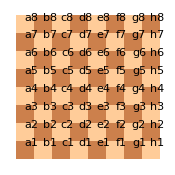
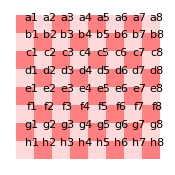
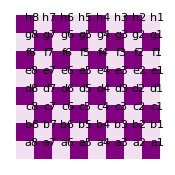
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{
	ChessPlot[cs0, ImageSize -> 175],
	ChessPlot[cs0, "WhiteOrientation" -> "Up",    "BoardColorSet" -> {White, Darker@Gray}, "ShowCoordinates" -> False, ImageSize -> 175],
	ChessPlot[cs0, "WhiteOrientation" -> "Left",  "BoardColorSet" -> {LightRed, Pink}, ImageSize -> 175],
	ChessPlot[cs0, "WhiteOrientation" -> "Right", "BoardColorSet" -> {LightPurple, Purple}, ImageSize -> 175]
}
```

You can double check orientation using the following images:

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

### ChessMove

```mathematica
ChessMove[cm : __Rule][str_?StringQ] := 
	Switch[str,
		"From",
			cm⟦1⟧
		,
		"To",
			cm⟦2⟧
		,
		_,
			Print["Try \"From\" or \"To\"."]; Return[$Failed];
	]

ChessMove /: MakeBoxes[cm : ChessMove[__Rule], StandardForm] := 
	Module[{icon},
		icon = 
			ToBoxes[
				ImageResize[
					pieceObj[♝]["Image"]
					, 
					150
				]
		];
			
		InterpretationBox @@ 
			{
				RowBox[{"ChessMove", "[", icon, "]"}],
			cm
			}
	]
```

Example of using ChessMove:

```mathematica
mv1 = ChessMove["a1" -> "b2"]
mv1["From"]
mv1["To"]
```

ChessMove[-Graphics-]

a1

b2

### ChessPlay

```mathematica
ChessPlay[chessHistory_, ChessMoves:{__ChessMove}] := 
	Module[{history = chessHistory, state, piece1, piece2},
		Do[
			state   = First[history⟦-1⟧];
		
			piece1  = state[move["From"]];
			piece2  = state[move["To"]];
			
			If[MemberQ[{♔, ♕, ♖, ♗, ♘, ♙}, piece2], AppendTo[state["WhiteCemetery"], piece2]];
			If[MemberQ[{♚, ♛, ♜, ♝, ♞, ♟}, piece2], AppendTo[state["BlackCemetery"], piece2]];
			
			state[move["From"]] = □;
			state[move["To"]] = piece1;
			
			AppendTo[history, ChessState[state]];
			,
			{move, ChessMoves}
		];
		history
	]
```

```mathematica
(* For notebook only *)
chessHistory = {cs0};
moves = ChessMove/@{"g1" -> "f3", "f7" -> "f5", "e2" -> "e4"};
chessHistory = ChessPlay[{cs0}, moves]
chessAnimate[chessHistory_] := Animate[Grid[{{ChessPlot[cs], ChessPlot[cs, "MatrixForm"-> True]}}], {cs, chessHistory},AnimationRate->2, SaveDefinitions->False]
chessAnimate@chessHistory
```

{ChessState[-Graphics-],ChessState[-Graphics-],ChessState[-Graphics-],ChessState[-Graphics-]}

## Chess Rules

The goal is to list all the possible moves, the moves that are according to the specified rules and not in contradiction with any of them.
To do this, we scan all the squares and list all the possible moves from it.

pos_1= {rank, file} represents the matrix coordinate in current player’s frame of reference
When a piece legally moves to an occupied square by the opponent, the opponents piece is captures.
Captured pieces go to their corresponding cemetery.
If S(pos_♔) == † with no legal moves (, the result is set to “0-1” and game ends.
If S(pos_♔) ≠ † with no legal moves, the game ends as “1/2-1/2”.


A. □
	1. No possible moves from it.
B. ♔ KingRestrictoins
	1. Eliminate all moves that result in S(pos_♔) == †.
C. ♙ PawnMoves
	1. May move to pos_2 = pos_1 + {1, 0} if S(pos_2)== □ & pos_2 < {8, ∀}
	2. May move to pos_2 = pos_1 + {0, +2} if pos_1 == {∀, 2} & S(pos_2 + {0, -1} )== □ & S(pos_2)== □.
	3. May move to pos_2 = pos_1 + ∀{{1, 0}, {±1, +1}} as ∀{♕, ♖, ♗, ♘} if pos_2 == {8, ∀} & S(pos_2)== {♛, ♜, ♝, ♞, ♟, □}.
	5. May move to pos_2= pos_1 + ∀{{±1, +1}} if S_-1(pos_2) == ♟ & S(pos_2 - {0, 2}) == ♟ and capture pos_2 - {0, 2}.
D. ♘ KnightMoves
	1. May move to pos_2 = pos_1 + ∀{{±1, ±2}, {±2, ±1}} if S(pos_2)== ∀{♛, ♜, ♝, ♞, ♟, □}.
E. ♗ BishopMoves
	1. For dir= ∀{±1, ±1} and n = ∀{1, ..., 8-1}, may move to pos = pos_0 + n ×dir if S(pos)== ∀{♛, ♜, ♝, ♞, ♟, □} and  S(pos_0 + {1, ..., n-1}dir) == □.
F. ♖ RookMoves
	1. For dir= ∀{{±1, 0}, {0, ±1}} and n = ∀{1, ..., 8-1}, may move to pos = pos_0 + n ×dir if S(pos)== ∀{♛, ♜, ♝, ♞, ♟, □} and  S(pos_0 + {1, ..., n-1}dir) == □.
G. ♕ QueenMoves
	1. For dir= ∀{{±1, 0}, {0, ±1}, {±1, ±1}} and n = ∀{1, ..., 8-1}, may move to pos = pos_0 + n ×dir if S(pos)== ∀{♛, ♜, ♝, ♞, ♟, □} and  S(pos_0 + {1, ..., n-1}dir) == □.
H. ♔ KingMoves
	1. For dir= ∀{{±1, 0}, {0, ±1}, {±1, ±1}}, may move to pos_2 = pos_1 + dir if S(pos_2)== ∀{♛, ♜, ♝, ♞, ♟, □}. 
	2. May {e1 → □, h1 → □, f1 → ♖, g1 → ♔} if f1 & g1 == □ & S(e1) ≠ † & S_i(e1) == ♔ for all i < t & S_i(h1) == ♖ for all i < t.
	3. May {e1 → □, a1 → □, d1 → ♖, c1 → ♔} if b1, c1, d1 == □ & S("e1") ≠ † & S_i("e1") == ♔ for all i < t & S_i("a1") == ♖ for all i < t.
	 -Graphics-

```mathematica
chessHistory
```

{ChessState[-Graphics-],ChessState[-Graphics-],ChessState[-Graphics-],ChessState[-Graphics-]}

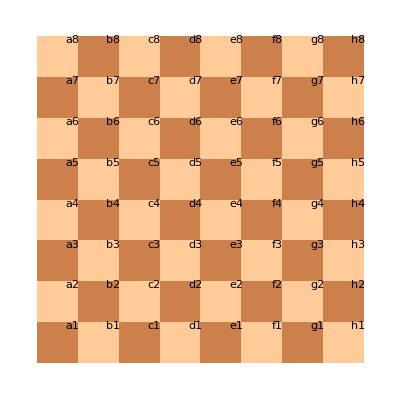
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fp /@ chessHistory
```

### A. Empty Square □

#### A1. No possible actions.

```mathematica
inRangeQ[pos_] :=
	Module[{cond1, cond2},
	cond1 = (1 ≤ pos⟦1⟧ ≤ rankSize);
	cond2 = (1 ≤ pos⟦2⟧ ≤ fileSize);
	Return[(cond1 ∧ cond2)];
	]
```

### B. Pawn ♙

#### B1. Ranking pos1 = the position of any ♙ pos2 = pos1 + {1, 0} cond1 = (rank of pos2 == rankSize) cond2 = (S(pos2) == □) ------------------------------------------------------------------------------------------ If !cond1 & cond2: pos1 → □ pos2 → ♙ If cond1 & cond2: pos1 → □ pos2 → ∀{♕, ♖, ♗, ♘}

```mathematica
B1[ch_] :=
	Module[{S = First[Last[ch]], actions, turn, piece, pos1List, coordMatrix, pos1, pos2, pos3, coord2, cond1, cond2, act1, act2},
		actions = {};
		(* Whose turn is it? *)
		turn = Mod[Length@ch + 1, 2] + 1;
		piece = Part[{♙, ♟}, turn];
		coordMatrix = Part[{wcm, bcm}, turn];
		
		pos1List = Position[S, piece][[All, 1, 1]];
		
		Do[
			pos1 = Position[coordMatrix, coord1]//First;
			
			pos2  = pos1 + {1, 0};
			If[!inRangeQ[pos2], Break[];];
			coord2 = Extract[coordMatrix, pos2];
			
			(* The case for going to the last rank *)
			cond1 = pos1⟦1⟧ == rankSize;
			(* The square in front of it must be empty *)
			cond2 = S[coord2] == □;
			(* Move from coord1 to coord2 *)
			act1 = (coord1 -> □);
			act2 = (coord2 -> piece);
			
			If[!cond1 ∧ cond2, 
				AppendTo[actions, {act1, act2}];
			];
						
			If[cond1 ∧ cond2, 
				AppendTo[actions, {coord1 -> □, coord1 -> Part[{♕, ♛}, turn]}];
				AppendTo[actions, {coord1 -> □, coord1 -> Part[{♖, ♜}, turn]}];
				AppendTo[actions, {coord1 -> □, coord1 -> Part[{♗, ♝}, turn]}];
				AppendTo[actions, {coord1 -> □, coord1 -> Part[{♘, ♞}, turn]}];
			];
			,
			{coord1, pos1List}
		];
		actions = DeleteDuplicates @ actions;
		Return[actions];
	]
```

```mathematica
B1[chessHistory]
```

{{a7→□,a6→♟},{b7→□,b6→♟},{c7→□,c6→♟},{d7→□,d6→♟},{e7→□,e6→♟},{g7→□,g6→♟},{h7→□,h6→♟},{f5→□,f4→♟}}

#### B2. Opening pos1 = the position of any ♙ pos2 = pos1 + {2, 0} cond1 = (rank of pos1 == 2) cond2 = (S(pos1 + {1, 0}) == □) cond3 = (S(pos2) == □) ------------------------------------------------------------------------------------------ If cond1 & cond2 & cond3: pos1 → □ pos2 → ♙

```mathematica
(* May move from pos1 to pos2 = pos1 + {+2, 0} if pos1 == {2, ∀} & S(pos1 + {+1, 0} )== □ & S(pos2)== □. *)
B2[ch_] :=
	Module[{S = First[Last[ch]], actions, turn, piece, pos1List, coordMatrix, pos1, pos2, pos3, coord2, coord3, cond1, cond2, cond3, act1, act2},
		actions = {};
		(* Whose turn is it? *)
		turn = Mod[Length@ch + 1, 2] + 1;
		piece = Part[{♙, ♟}, turn];
		coordMatrix = Part[{wcm, bcm}, turn];
		
		pos1List = Position[S, piece][[All, 1, 1]];
		
		Do[
			pos1 = Position[coordMatrix, coord1]//First;
			
			pos2  = pos1 + {+1, 0};
			coord2 = Extract[coordMatrix, pos2];
			
			pos3  = pos2 + {+1, 0};
			coord3 = Extract[coordMatrix, pos3];
			
			(* Must be at rank 2 *)
			cond1 = pos1⟦1⟧ == 2;
			(* The two squares in front of it must be empty *)
			cond2 = S[coord2] == □;
			cond3 = S[coord3] == □;
			
			act1 = (coord1 -> □);
			act2 = (coord3 -> piece);
			
			If[cond1 ∧ cond2 ∧ cond3, 
				AppendTo[actions, {act1, act2}];
			];
			,
			{coord1, pos1List}
		];
		actions = DeleteDuplicates @ actions;
		Return[actions];
	]
```

```mathematica
B2[chessHistory ]
```

{{a7→□,a5→♟},{b7→□,b5→♟},{c7→□,c5→♟},{d7→□,d5→♟},{e7→□,e5→♟},{g7→□,g5→♟},{h7→□,h5→♟}}

#### B3. Capturing: A pawn may move from pos1 to pos2 = pos1 + ∀{{±1, +1}} if S(pos1) == ∀{♛, ♜, ♝, ♞, ♟} & rank of pos2 ≠ rankSize pos1 = the position of any ♙ pos2 = pos1 + ∀{{1, ±1}} cond1 = (rank of pos2 == rankSize) cond2 = (S(pos2) == ∀{♛, ♜, ♝, ♞, ♟}) ------------------------------------------------------------------------------------------ If !cond1 & cond2: pos1 → □ pos2 → ♙ ∀{♛, ♜, ♝, ♞, ♟} → blackCemetery If cond1 & cond2: pos1 → □ pos2 → ∀{♕, ♖, ♗, ♘} ∀{♛, ♜, ♝, ♞, ♟} → blackCemetery

```mathematica
B3[ch_] :=
	Module[{S = First[Last[ch]], actions, turn, piece, pos1List, steps, coordMatrix, pos1, pos2, pos3, coord2, coord3, cond1, cond2, opponentCemetery, opponentPieces},
		actions = {};
		(* Whose turn is it? *)
		turn = Mod[Length@ch + 1, 2] + 1;
		piece = Part[{♙, ♟}, turn];
		(* Rest is to remove the king *)
		opponentPieces = Part[{Rest @ blackPieces, Rest @ whitePieces}, turn];
		opponentCemetery =  Part[{"blackCemetery", "whiteCemetery"}, turn];
		coordMatrix = Part[{wcm, bcm}, turn];
		
		pos1List = Position[S, piece][[All, 1, 1]];
		steps = {{1, -1}, {1, +1}};
		
		Do[
			pos1 = Position[coordMatrix, coord1]//First;
			Do[
				pos2  = pos1 + step;
				If[!inRangeQ[pos2], Continue[];];
				coord2 = Extract[coordMatrix, pos2];
				
				(* Must be at rank 2 *)
				cond1 = pos2⟦1⟧ == rankSize;
				(* The two squares in front of it must be empty *)
				cond2 = MemberQ[opponentPieces, S[coord2]];
				If[!cond1 ∧ cond2, 
					AppendTo[actions, {coord1 -> □, S[coord2] -> opponentCemetery, coord2 -> piece}];
				];
							
				If[cond1 ∧ cond2, 
					AppendTo[actions, {coord1 -> □, S[coord2] -> opponentCemetery, coord2 -> Part[{♕, ♛}, turn]}];
					AppendTo[actions, {coord1 -> □, S[coord2] -> opponentCemetery, coord2 -> Part[{♖, ♜}, turn]}];
					AppendTo[actions, {coord1 -> □, S[coord2] -> opponentCemetery, coord2 -> Part[{♗, ♝}, turn]}];
					AppendTo[actions, {coord1 -> □, S[coord2] -> opponentCemetery, coord2 -> Part[{♘, ♞}, turn]}];
				];
			,
			{step, steps}
			];
			,
			{coord1, pos1List}
		];
		actions = DeleteDuplicates @ actions;
		Return[actions];
	]
	
B3[chessHistory ]
```

{{f5→□,♙→whiteCemetery,e4→♟}}

#### B4. En Passant pos1 = the position of any ♙ pos2 = pos1 + ∀{{±1, +1}} pos3 = pos2 - {2, 0} cond1 = (rank of pos2 == rankSize) cond2 = (S_-2(pos2) == ♟) cond3 = (S(pos3) == ♟) ------------------------------------------------------------------------------------------ If cond1 & cond2 & cond3: pos1 → □ ♟→ blackCemetery pos2 → ♙

```mathematica
B4[ch_] := 
	Module[{},
		Print["NOT IMPLEMENTED"];
		Return[{}]
	]
```

### C. Knight ♘

#### C1. May move to pos = pos_0 + ∀{{±1, ±2}, {±2, ±1}} if S(pos)== ∀{♛, ♜, ♝, ♞, ♟, □}. pos1 = the position of any ♘ pos2 = pos1 + ∀{{±1, ±2}, {±2, ±1}} cond1 = (S(pos2) == ∀{♛, ♜, ♝, ♞, ♟, □}) ------------------------------------------------------------------------------------------ If cond1: pos1 → □ ∀{♛, ♜, ♝, ♞, ♟, □} → blackCemetery pos2 → ♘

```mathematica
C1[ch_] :=
	Module[{S = First[Last[ch]], actions, turn, piece, pos1List, steps, coordMatrix, pos1, pos2, pos3, coord2, coord3, cond1, cond2, opponentCemetery, opponentPieces},
		actions = {};
		(* Whose turn is it? *)
		turn = Mod[Length@ch + 1, 2] + 1;
		piece = Part[{♘, ♞}, turn];
		(* Rest is to remove the kings *)
		opponentPieces = Part[{Rest @ blackPieces, Rest @ whitePieces}, turn];
		opponentCemetery =  Part[{"blackCemetery", "whiteCemetery"}, turn];
		coordMatrix = Part[{wcm, bcm}, turn];
		
		pos1List = Position[S, piece][[All, 1, 1]];
		steps = {{-2, -1}, {-2, +1}, {-1, -2}, {-1, +2}, {+1, -2}, {+1, +2}, {+2, -1}, {+2, +1}};
		
		Do[
			pos1 = Position[coordMatrix, coord1]//First;
			Do[
				pos2  = pos1 + step;
				If[!inRangeQ[pos2], Continue[];];
				coord2 = Extract[coordMatrix, pos2];
				(* The two squares in front of it must be empty *)
				cond1 = MemberQ[opponentPieces ~Join~ {□}, S[coord2]];

				If[cond1 ∧ S[coord2] == □, 
					AppendTo[actions, {coord1 -> □, coord2 -> piece}];
				];
				If[cond1 ∧ S[coord2] ≠ □,
					AppendTo[actions, {coord1 -> □, S[coord2] -> opponentCemetery, coord2 -> piece}];
				]
				,
				{step, steps}
			];
			,
			{coord1, pos1List}
		];
		actions = DeleteDuplicates @ actions;
		Return[actions];
	]
```

```mathematica
C1[chessHistory]
```

{{b8→□,a6→♞},{b8→□,c6→♞},{g8→□,f6→♞},{g8→□,h6→♞}}

```mathematica
fp/@chessHistory
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## ChessPlay 2!

```mathematica
ChessEvolve[chessHistory_, actions:{__Rule}] := 
	Module[{S = First[Last[chessHistory]]},
		Do[
			S[action⟦1⟧] = action⟦2⟧;
			,
			{action, actions}
		];
		Return[chessHistory ~Join~ {ChessState[S]}];
	]
```

```mathematica
possibleActions = C1[chessHistory];
variations = ChessEvolve[chessHistory, #]&/@possibleActions;
Animate[Grid[{{ChessPlot[cs], ChessPlot[cs, "MatrixForm"-> True]}}], {cs, {Last[chessHistory]}~Join~Riffle[variations[[All,-1]],Last[chessHistory]]~Join~{Last[chessHistory]}},AnimationRate->1.5, SaveDefinitions->False]
```

## Game PGN

```mathematica
gameString = "1. e4 e5 2. Nf3 Nc6 3. Nc3 Nf6 4. Bb5 Bb4 5. O-O O-O 6. d3 Bxc3 7. bxc3 d6 8.
Bg5 Bd7 9. Nd2 h6 10. Bh4 g5 11. Bg3 Ne7 12. Bxd7 Nxd7 13. d4 f5 14. exf5 exd4
15. cxd4 Nxf5 16. Qf3 Rf7 17. Qxb7 Nxd4 18. Qe4 Nf5 19. Rae1 Qc8 20. f4 Nf6 21.
Qd3 g4 22. Bf2 Qd7 23. Bd4 Nxd4 24. Qxd4 Qb5 25. Kh1 Qd5 26. Qf2 Qxa2 27. Nb3 a5
28. Ra1 Qb2 29. Nxa5 Qc3 30. Nb3 Rxa1 31. Nxa1 Nd5 32. g3 Re7 33. Nb3 Re3 34.
Rd1 Nf6 35. Nd2 Qxc2 36. Qxe3 Qxd1+ 37. Kg2 Kf7 38. f5 Qa1 39. Qxh6 Qd4 40. Qg6+
Ke7 41. Qg7+ Ke8 42. Qg5 Qd5+ 43. Kg1 Kf7 44. Qg6+ Ke7 45. Qg7+ Qf7 46. Qg5 Qd5
47. Qg7+ Qf7 48. Qg5 Qd5 49. Qg7+ 1/2-1/2";

(* Remove newline *)
gameString = StringReplace[gameString,{"\n" -> " "}];

(* Remove game result *)
gameResultStrings = {"1-0", "0-1", "1/2-1/2"};
gameString = StringSplit[gameString, gameResultStrings]⟦1⟧;

(* Splite to turns *)
gs = StringSplit[gameString, DigitCharacter..~~"."];

(* Splite to moves *)
gs = StringSplit[#,WhitespaceCharacter]&/@ gs;
TableView[gs]
```

e4e5Nf3Nc6Nc3Nf6Bb5Bb4O-OO-Od3Bxc3bxc3d6Bg5Bd7Nd2h6Bh4g5Bg3Ne7Bxd7Nxd7d4f5exf5exd4cxd4Nxf5Qf3Rf7Qxb7Nxd4Qe4Nf5Rae1Qc8f4Nf6Qd3g4Bf2Qd7Bd4Nxd4Qxd4Qb5Kh1Qd5Qf2Qxa2Nb3a5Ra1Qb2Nxa5Qc3Nb3Rxa1Nxa1Nd5g3Re7Nb3Re3Rd1Nf6Nd2Qxc2Qxe3Qxd1+Kg2Kf7f5Qa1Qxh6Qd4Qg6+Ke7Qg7+Ke8Qg5Qd5+Kg1Kf7Qg6+Ke7Qg7+Qf7Qg5Qd5Qg7+Qf7Qg5Qd5Qg7+

```mathematica
Map[Association@Thread[If[Length[#]==2,{"White","Black"},{"White"}]->#]&,gs]
```

{<|White→e4,Black→e5|>,<|White→Nf3,Black→Nc6|>,<|White→Nc3,Black→Nf6|>,<|White→Bb5,Black→Bb4|>,<|White→O-O,Black→O-O|>,<|White→d3,Black→Bxc3|>,<|White→bxc3,Black→d6|>,<|White→Bg5,Black→Bd7|>,<|White→Nd2,Black→h6|>,<|White→Bh4,Black→g5|>,<|White→Bg3,Black→Ne7|>,<|White→Bxd7,Black→Nxd7|>,<|White→d4,Black→f5|>,<|White→exf5,Black→exd4|>,<|White→cxd4,Black→Nxf5|>,<|White→Qf3,Black→Rf7|>,<|White→Qxb7,Black→Nxd4|>,<|White→Qe4,Black→Nf5|>,<|White→Rae1,Black→Qc8|>,<|White→f4,Black→Nf6|>,<|White→Qd3,Black→g4|>,<|White→Bf2,Black→Qd7|>,<|White→Bd4,Black→Nxd4|>,<|White→Qxd4,Black→Qb5|>,<|White→Kh1,Black→Qd5|>,<|White→Qf2,Black→Qxa2|>,<|White→Nb3,Black→a5|>,<|White→Ra1,Black→Qb2|>,<|White→Nxa5,Black→Qc3|>,<|White→Nb3,Black→Rxa1|>,<|White→Nxa1,Black→Nd5|>,<|White→g3,Black→Re7|>,<|White→Nb3,Black→Re3|>,<|White→Rd1,Black→Nf6|>,<|White→Nd2,Black→Qxc2|>,<|White→Qxe3,Black→Qxd1+|>,<|White→Kg2,Black→Kf7|>,<|White→f5,Black→Qa1|>,<|White→Qxh6,Black→Qd4|>,<|White→Qg6+,Black→Ke7|>,<|White→Qg7+,Black→Ke8|>,<|White→Qg5,Black→Qd5+|>,<|White→Kg1,Black→Kf7|>,<|White→Qg6+,Black→Ke7|>,<|White→Qg7+,Black→Qf7|>,<|White→Qg5,Black→Qd5|>,<|White→Qg7+,Black→Qf7|>,<|White→Qg5,Black→Qd5|>,<|White→Qg7+|>}

## Carlo’s Notes

```mathematica
ChessState[a_?AssociationQ][s_?StringQ] /; StringMatchQ[s, LetterCharacter~~DigitCharacter];
ChessState[state]["a1"];
```

Carlo’s Idea:

```mathematica
wki=pieceObj[♔]["Image"];
	bki=pieceObj[♚]["Image"];
	
	pi = {wki, bki};

	pPos = {{1,1},{2,3}};
	
	LocatorPane[
		Dynamic[pPos],
		ap,
		Appearance -> pi];
```

```mathematica
(* DELETE, From Carlo
$piecesPattern = Alternatives @@ Most[pieceSymbols];
ChessState[a : {__Rule}] := ChessState[Association[a]] 
ChessState[a_?AssociationQ][pos_?StringQ] /; StringMatchQ[pos, files ~~ ranks] := Lookup[a, pos, □]
cs_ChessState[x_?StringQ, y_?StringQ] := cs[x <> y]
cs_ChessState[x_?IntegerQ, y_?IntegerQ] := cs[files[[x]], ToString[y]]

cs_ChessState[s_?StringQ] /; StringMatchQ[s, $piecesPattern] := 
	Replace[
		Position[First[cs], s],
		{
			{} -> {},
			any_ :> any[[All, 1, 1]]
		}
	]

cs_ChessState["ChessPlot", opts___] := ChessPlot[First[cs], opts]

ChessState /: MakeBoxes[cs_ChessState, StandardForm] := 
	Module[{},
		icon = 
			ToBoxes[
				ImageResize[
					pieceObj[♞]["Image"]
					, 
					150
				]
			];
			
		InterpretationBox @@ 
			{
				RowBox[{"ChessState", "[", icon, "]"}],
				cs
			}
	]



initialChessState = ChessState[initialChessStateList]
cs0 = initialChessState;
*)
```